```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_312run3.txt","Table"];
```

```mathematica
Dimensions[Take[rawdata,17243]]
```

{17243}

```mathematica
rawdata=Drop[rawdata,{17243}];
```

```mathematica
Dimensions[rawdata]
```

{28589,3}

```mathematica
num=Dimensions[rawdata][[1]]
```

28589

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
timevolt=Table[0,{i,num}];
Do[timevolt[[i]]=Flatten[{time[[i]],voltage[[i]]},2],{i,1,num}]
```

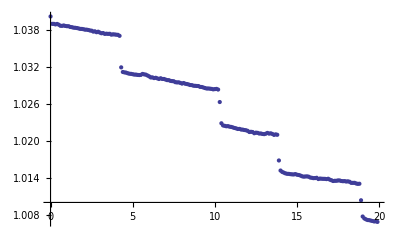

```mathematica
ListPlot[Take[timevolt,{1,200}]]
```

```mathematica
threshold=.003;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,num-7}]
```

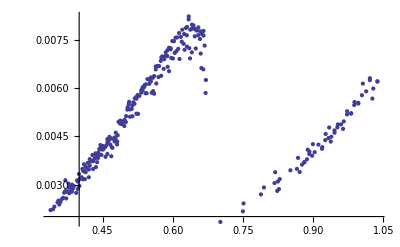

```mathematica
ListPlot[dT]
```